## Úkol 10.1

```mathematica
Limit[(Sin[x]/Sin[a])^(1/(x-a)),x->a]
```

ⅇ^Cot[a]

## Úkol 10.2

```mathematica
f=Integrate[√(1+x^4),x]
```

(x+x^5-2 (-1)^(1/4) √(1+x^4) EllipticF[ⅈ ArcSinh[(-1)^(1/4) x],-1])/(3 √(1+x^4))

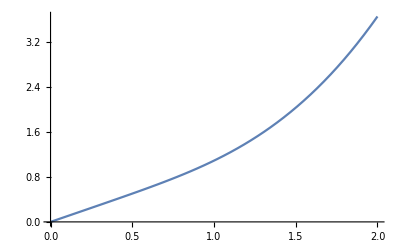

```mathematica
Plot[f,{x,0,2}]
```

## Úkol 10.3

```mathematica
exact=DSolve[{y''[t]==-Sin[y[t]],y[0]==0,y'[0]==1},y[t],t]
```

{{y[t]→2 JacobiAmplitude[t/2,4]}}

```mathematica
approximate=DSolve[{y''[t]==-y[t],y[0]==0,y'[0]==1},y[t],t]
```

{{y[t]→Sin[t]}}

```mathematica
Plot[{y[t]/.exact,y[t]/.approximate},{t,0,20},PlotLabels->{"Exact","Approximate"},AxesLabel->{"t","y"}]
```

-Graphics-